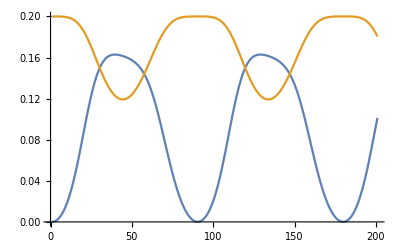

```mathematica
ClearAll["Global`*"];
qubitmatrixToCartesian[Mq_]:=(
q1=Re[(Mq[[1,2]]+Mq[[2,1]])/2];
q2=Re[(Mq[[2,1]]-Mq[[1,2]])/(2*I)];
q3=Re[Mq[[1,1]]];
Return[{q1,q2,q3}];
);

rnSU2euler[vec_,rx_,ry_,rz_]:=(
sphericalVec = ToSphericalCoordinates[vec];
θ=sphericalVec[[2]];
ϕ=sphericalVec[[3]];
sx=PauliMatrix[1];
sy=PauliMatrix[2];
sz=PauliMatrix[3];
Mq=Sin[θ]*Cos[ϕ]*sx+Sin[θ]*Sin[ϕ]*sy+Cos[θ]*sz;
Un={{Exp[-I*(rx+rz)/2]*Cos[ry/2],-Exp[-I*(rx-rz)/2]*Sin[ry/2]},{Exp[I*(rx-rz)/2]*Sin[ry/2],Exp[I*(rx+rz)/2]*Cos[ry/2]}};
Return [Un.Mq.ConjugateTranspose[Un]];
);

rotateVector[vec_,rx_,ry_,rz_]:=(
MqRotated=rnSU2euler[vec,rx,ry,rz];
Return[qubitmatrixToCartesian[MqRotated]];
);
subtractAngles[a1_,a2_]:=(
d=Abs[a1-a2];
Return[Min[d,2*Pi-d]];
);
errorPropagation[n_,vec_,vecError_,rx_,ry_,rz_]:=(
(*v=NestList[N[rotateVector[#,rx,ry,rz]]&,vec,n];
vErr=NestList[N[rotateVector[#,rx,ry,rz]]&,vecError,n];*)
v=NestList[rotateVector[#,rx,ry,rz]&,N@vec,n];
vErr=NestList[rotateVector[#,rx,ry,rz]&,N@vecError,n];
polar=Map[ToSphericalCoordinates,v];
polarErr=Map[ToSphericalCoordinates,vErr];
{MapThread[subtractAngles,{polarErr[[All,3]],polar[[All,3]]}],MapThread[subtractAngles,{polarErr[[All,2]],polar[[All,2]]}]}
);

ListLinePlot[errorPropagation[200,{1,0,0},N[rotateVector[{1,0,0},0,0.2,0]],Pi/100,Pi/100,Pi/100]]
```